```mathematica
Module[
{height=1000, start, top},
With[
{all=Select[
Sort[Subsets[Prime[Range[2,25]],{6}],N[magicGraham[#1]] >N[ magicGraham[#2]]&],
N[magicGraham[#]]<0.001&]},
start=0;
top=10^100;
Monitor[
Table[
CalcGoodForTuple[all[[pos]],height+Quotient[Min[all[[pos]]]+1,2],start,top],
{pos,1,Length[all]}
],
{pos,Length[all],all[[pos]],N[magicGraham[all[[pos]]]], height, N[Log[10,start+1]->Log[10,top]]}
]
]
]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

Aborted at value : 943

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-3996
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-4414
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-4487
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-6403
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-6549
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-6669
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-6874
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\7\41\59\Solutions.txt.78.431%.-7030
```

```mathematica
78.431%.-9069
```

```mathematica
78.431%.-9453
```

```mathematica
78.431%.-9605
```

```mathematica
78.431%.-9705
```

```mathematica
78.431%.-10155
```

```mathematica
78.431%.-10209
```

```mathematica
78.431%.-10244
```

```mathematica
CloseStreams[]
```

Closing d:\triangle\DataSrc\37\59\61\67\Solutions.txt

Closing d:\triangle\DataSrc\23\47\59\67\Solutions.txt

```mathematica
Length[GoodForTuple[{5,7,23,37}]]
```

1005

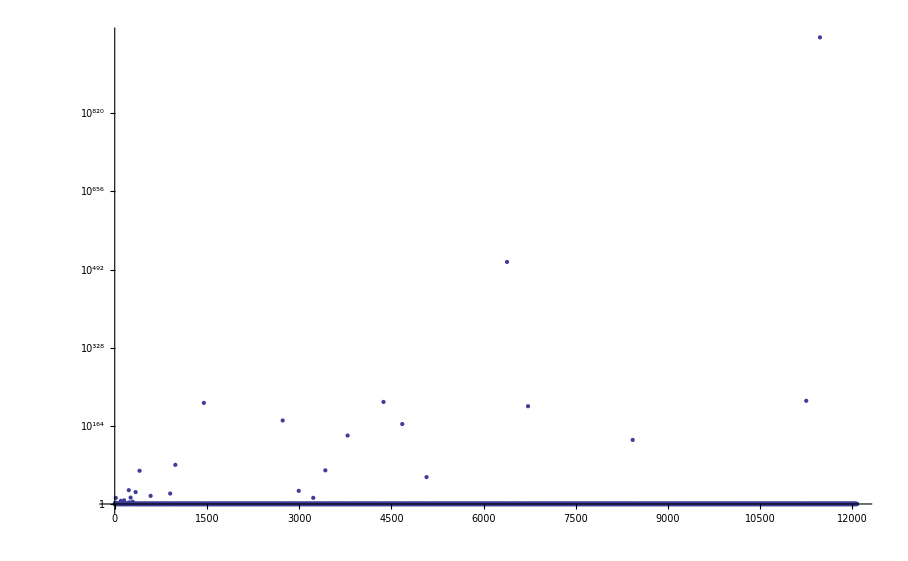

```mathematica
ListLogPlot[Ratios[Rest[GoodForTuple[{3,31,43,173,229}]]]]
```

```mathematica
t=N[Log[Differences[GoodForTuple[{3,5,7,Prime[15518428738-1]}]]]]
```

{0.,2.19722,6.61473,0.,7.78447,3.2581,0.,4.14313,8.36869,0.,4.49981,9.4219,17.902,3.17805,24.5457,14.3946,37.7573,0.,1.60944,19.5022,0.,4.72739,15.5825,9.5699,3.3322,30.2383,0.,2.99573,0.,6.58617,1.09861,1.79176,0.,9.83199,5.49306,0.,41.0132,17.6607,7.65681,9.72657,11.93,2.19722,24.1852,0.,4.48864,0.,13.6037,0.,1.60944,0.,3.78419,1.38629,5.2832,3.7612,2.48491,61.5641,3.17805,35.5634,0.,3.13549,11.2838,0.693147,8.74114,4.14313,0.,19.3113,0.,5.85793,0.,11.2537,2.19722,0.,18.6648,0.693147,5.03044,0.,1.60944,0.,9.87504,0.,69.2526,0.,6.55251,3.68888,49.8363,0.,40.5316,0.,6.42972,0.,2.07944,0.,16.1034,74.8406,0.,100.016,0.,7.02554,24.1046,0.,2.07944,14.6057,49.3175,0.,1.60944,0.,21.6189,0.,4.7362,8.04751,2.19722,38.8518,0.693147,9.82919,57.1332,15.7664,0.,1.60944,4.59512,0.,5.15329,0.,30.3179,0.,7.7803,0.,1.79176,1.09861,67.7626,2.19722,3.21888,24.1318,0.693147,15.3809,0.,1.60944,6.43615,0.,102.203,129.638,2.99573,0.,6.58617,0.,14.3285,0.,6.60665,65.0497,0.,35.721,1.79176,46.6726,0.693147,7.99058,3.91202,41.6414,0.,16.6786,0.,1.60944,0.,3.78419,1.38629,5.2832,4.00733,7.95472,0.,33.8039,12.3988,17.6136,0.,5.47646,1.38629,162.611,3.66356,0.,5.31812,3.2581,0.,6.00389,7.79893,0.,22.0209,10.3971,11.8267,2.70805,102.067,0.,8.11522,1.09861,10.9219,0.,19.2956,2.99573,0.,18.6702,0.,1.60944,3.3322,0.693147,10.2653,0.,1.60944,66.7689,0.693147,5.49306,0.,1.79176,8.7971,1.09861,3.2581,0.,6.54103,1.60944,0.,35.012,1.79176,6.6174,0.693147,9.83975,3.3322,1.79176,36.9987,9.42416,0.,5.49306,0.693147,19.1897,171.397,0.,44.9981,25.4123,3.04452,107.85,0.,2.07944,0.,9.86765,6.44572,4.58497,0.,15.6456,0.,9.76904,0.693147,35.7381,1.09861,9.84453,0.,6.38012,1.38629,4.83628,3.17805,20.0904,0.,7.11477,1.09861,4.94164,105.079,118.26,0.693147,3.3322,70.8104,73.8173,0.,153.688,0.,13.0514,1.09861,230.863,0.,13.1696,3.68888,8.38046,0.,12.3484,8.6125,0.693147,42.9603,0.,16.1043,5.03044,0.,13.8765,19.3087,4.39445,0.,2.99573,6.44572,7.45298,3.8712,0.,48.6419,0.693147,25.5661,66.0215,0.,16.0928,14.159,0.,7.78322,1.09861,4.75359,0.,20.6053,2.19722,3.2581,0.,8.38252,1.38629,46.6633,6.61607,1.09861,19.2991,0.693147,282.46,3.7612,2.48491,348.38,0.,6.5903,0.,17.6483,3.91202,0.,75.5576,0.,3.91202,31.858,1.79176,5.04343,0.,12.0934,0.,192.22,0.,1.79176,7.80384,12.3658,3.13549,0.,22.6675,0.,38.4321,423.363,0.,9.42577,0.,6.57786,0.,8.7352,188.753,0.,1.60944,1.09861,7.85941,23.8693,2.19722,7.71423,0.,5.0814,11.614,2.19722,35.1971,491.133,1.09861,4.94164,6.37161,0.,8.25946,1.79176,12.0457,6.47851,27.3751,0.,4.77912,69.1994,62.5832,0.,5.45104,3.68888,19.1447,0.693147,9.72699,0.,46.6631,37.67,49.3694,0.693147,4.82028,2.19722,19.2984,9.6418,8.74114,0.,4.17439,5.19296,0.,1.60944,35.1805,4.96981,0.,2.99573,0.,7.71824}

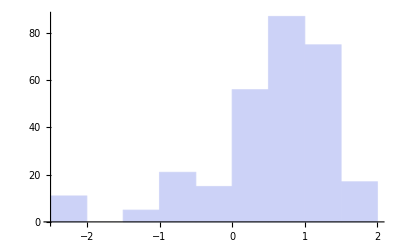

```mathematica
Histogram[Log[Log[t]],PlotRange->All]
```

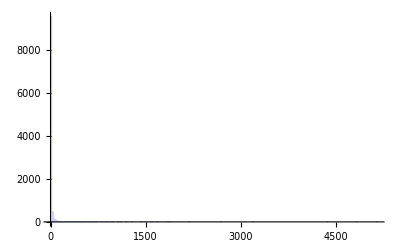

```mathematica
Histogram[t]
```

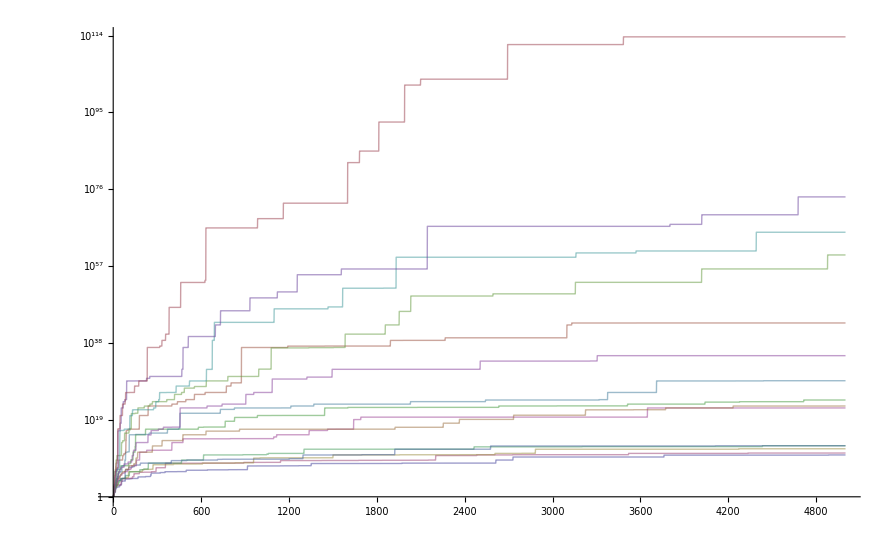

```mathematica
With[
{all=Sort[Select[
Prime[Subsets[Range[2,25,4],{4}]],
magicGraham[#]>0&],magicGraham[#1] > magicGraham[#2]&]},
ListLogPlot[Select[Table[FirstGood[tuple],{tuple,all}],# ≠ {}&],Joined->True,PlotStyle->Opacity[0.5]]
]
```

```mathematica
FirstGood[tuple_]:=
Module[
{good, limit=5000, result={},fileName= FileNameForTuple[tuple]},
If[FileExistsQ[fileName],
result= ReadList[fileName,Expression, limit];
];
result
]
```

```mathematica
Module[
{height=10000, start, top},
With[
{all=Sort[Subsets[Prime[Range[2,25]],{3}],N[magicGraham[#1]] >N[ magicGraham[#2]]&]},
start=0;
top=10^500;
Monitor[
Table[
CalcGoodForTuple[all[[pos]],height+Quotient[Min[all[[pos]]]+1,2],start,top],
{pos,1,Length[all],1}
],
{pos,Length[all],all[[pos]],N[magicGraham[all[[pos]]]], height, N[Log[10,start+1]->Log[10,top]]}
]
]
]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
CloseStreams[]
```

```mathematica
Clear[MyMaxValue2]
```

```mathematica
MyMaxValue2[tuple_,limit_]:=
Module[
{good, result=0,fileName= FileNameForTuple[tuple]},
If[FileExistsQ[fileName],
good= ReadList[fileName,Expression, limit];
If[Length[good] == limit,
result=Last[good];
MyMaxValue2[tuple,limit]=result
]
];
result
]
```

```mathematica
data=With[
{range=10000},
Table[
{N[magicGraham[tuple]],
N[Log[MyMaxValue2[tuple,range+Quotient[Min[tuple]+1,2]]]]},
{tuple,Subsets[Prime[Range[2,25]],{3}]}
]
]
```

{{0.0259503,194.742},{0.0607577,111.1},{0.0721904,98.9121},{0.0890598,72.8279},{0.0955474,72.615},{0.106045,61.8998},{0.117757,66.0669},{0.120932,57.1421},{0.128963,55.0692},{0.133373,53.1137},{0.135359,54.9802},{0.138973,51.6874},{0.143661,51.7555},{0.147666,54.9684},{0.148878,51.7554},{0.152209,48.3392},{0.154209,53.1305},{0.155152,48.3395},{0.15778,45.149},{0.159384,48.6311},{0.161603,47.3908},{0.164261,44.27},{0.0905659,78.122},{0.101999,68.1505},{0.118868,60.7146},{0.125356,64.9388},{0.135853,57.2772},{0.147565,49.8086},{0.15074,50.654},{0.158771,50.6563},{0.163181,42.9512},{0.165168,43.2146},{0.168781,44.055},{0.173469,43.9581},{0.177474,43.9628},{0.178687,42.9624},{0.182017,44.055},{0.184017,44.055},{0.18496,41.7615},{0.187588,41.7514},{0.189193,41.76},{0.191411,42.0665},{0.194069,37.7579},{0.136806,54.2083},{0.153675,48.3517},{0.160163,48.341},{0.17066,43.164},{0.182373,39.5625},{0.185548,39.8695},{0.193578,40.941},{0.197988,38.7705},{0.199975,38.7436},{0.203588,38.7525},{0.208276,37.4012},{0.212282,38.4933},{0.213494,37.3653},{0.216824,36.3043},{0.218824,37.3651},{0.219767,37.4705},{0.222395,37.4707},{0.224,37.3576},{0.226218,36.3043},{0.228876,34.4343},{0.165108,42.8842},{0.171596,42.896},{0.182093,38.771},{0.193805,38.4883},{0.196981,38.5619},{0.205011,36.3068},{0.209421,37.3589},{0.211408,37.7295},{0.215021,31.9762},{0.219709,34.1637},{0.223714,31.878},{0.224927,31.9134},{0.228257,31.1319},{0.230257,32.1749},{0.2312,32.2649},{0.233828,32.2307},{0.235433,33.3625},{0.237651,32.2649},{0.240309,29.6764},{0.188465,39.6935},{0.198962,39.8772},{0.210675,38.4557},{0.21385,35.4711},{0.22188,33.2839},{0.22629,38.7798},{0.228277,37.641},{0.231891,33.0085},{0.236578,32.9584},{0.240584,32.9767},{0.241796,33.2462},{0.245126,31.8643},{0.247126,31.9764},{0.248069,31.8657},{0.250697,32.9989},{0.252302,33.2595},{0.25452,30.0335},{0.257178,28.6852},{0.20545,39.9432},{0.217162,38.4696},{0.220338,34.3821},{0.228368,33.2835},{0.232778,34.2003},{0.234765,35.5322},{0.238378,33.1109},{0.243066,34.3447},{0.247071,34.0616},{0.248284,31.0792},{0.251614,30.8702},{0.253614,33.1109},{0.254557,33.2594},{0.257185,30.8708},{0.25879,29.8116},{0.261008,33.2584},{0.263666,28.6008},{0.22766,37.7542},{0.230835,30.0568},{0.238865,30.0429},{0.243275,30.0559},{0.245262,35.2724},{0.248875,32.2643},{0.253563,30.0429},{0.257569,30.0344},{0.258781,28.9582},{0.262111,32.1607},{0.264111,30.0331},{0.265054,32.1567},{0.267682,32.2316},{0.269287,29.6628},{0.271505,30.0417},{0.274163,28.5808},{0.242547,32.009},{0.250578,34.4532},{0.254987,32.1486},{0.256974,35.3048},{0.260588,31.158},{0.265275,31.0533},{0.269281,28.5776},{0.270493,31.9693},{0.273823,31.0892},{0.275824,31.05},{0.276766,28.8914},{0.279395,28.9433},{0.280999,31.0493},{0.283217,28.5644},{0.285876,28.5641},{0.253753,28.9654},{0.258163,28.9434},{0.26015,33.0072},{0.263763,29.8044},{0.268451,28.6845},{0.272456,27.518},{0.273668,27.5712},{0.276999,27.8708},{0.278999,27.5711},{0.279942,28.5816},{0.28257,28.7027},{0.284175,28.6061},{0.286393,28.6044},{0.289051,26.7461},{0.266193,27.8624},{0.26818,27.5036},{0.271793,28.9656},{0.276481,27.7928},{0.280487,26.6831},{0.281699,27.5036},{0.285029,26.4049},{0.287029,26.6909},{0.287972,27.6145},{0.2906,26.4048},{0.292205,26.7434},{0.294423,25.5846},{0.297081,25.5847},{0.27259,30.8108},{0.276203,28.9601},{0.280891,28.707},{0.284897,27.6047},{0.286109,27.6195},{0.289439,28.5694},{0.291439,28.5776},{0.292382,27.8615},{0.29501,27.8362},{0.296615,27.6157},{0.298833,28.5644},{0.301491,26.6912},{0.27819,27.7668},{0.282878,28.5762},{0.286883,27.4655},{0.288096,27.5036},{0.291426,26.3808},{0.293426,27.572},{0.294369,30.7994},{0.296997,26.4045},{0.298602,27.7572},{0.30082,25.5872},{0.303478,26.3832},{0.286491,28.578},{0.290497,25.6726},{0.291709,29.6626},{0.295039,25.4099},{0.297039,27.7834},{0.297982,28.9358},{0.30061,25.4066},{0.302215,25.5951},{0.304433,25.5876},{0.307091,24.5664},{0.295185,25.6358},{0.296397,28.8913},{0.299727,26.4721},{0.301727,26.4031},{0.30267,26.4772},{0.305298,25.2863},{0.306903,24.2222},{0.309121,25.639},{0.311779,25.2727},{0.300402,27.5141},{0.303733,25.3735},{0.305733,25.6361},{0.306676,27.5709},{0.309304,27.4654},{0.310908,25.6616},{0.313127,25.5865},{0.315785,24.5627},{0.304945,26.3667},{0.306945,27.5719},{0.307888,26.6578},{0.310516,25.4099},{0.312121,26.5157},{0.314339,27.7632},{0.316997,26.4848},{0.310275,24.4696},{0.311218,24.4976},{0.313846,25.4102},{0.315451,25.2724},{0.317669,25.4112},{0.320327,25.2727},{0.313218,26.4844},{0.315846,26.3709},{0.317451,25.5923},{0.319669,25.5961},{0.322327,24.5413},{0.316789,26.4725},{0.318394,26.5157},{0.320612,27.7576},{0.32327,26.5169},{0.321022,25.4074},{0.32324,24.5749},{0.325898,24.5629},{0.324845,25.2818},{0.327503,24.4976},{0.329721,24.2863},{0.142242,56.5909},{0.153675,47.5575},{0.170544,43.7166},{0.177032,50.7846},{0.187529,41.1322},{0.199242,37.2702},{0.202417,37.8107},{0.210447,34.2021},{0.214857,36.218},{0.216844,35.8104},{0.220457,35.4178},{0.225145,34.1929},{0.229151,33.8069},{0.230363,33.9872},{0.233693,32.3796},{0.235693,32.2433},{0.236636,32.3727},{0.239264,31.3931},{0.240869,32.3744},{0.243087,33.0811},{0.245745,33.8454},{0.188482,42.1957},{0.205352,38.6351},{0.211839,37.421},{0.222337,36.2907},{0.234049,32.3859},{0.237224,32.5661},{0.245255,31.3754},{0.249665,32.5661},{0.251651,31.2782},{0.255265,32.2808},{0.259953,32.5824},{0.263958,31.2776},{0.26517,29.0502},{0.268501,29.6728},{0.270501,29.049},{0.271444,28.0737},{0.274072,29.0184},{0.275676,29.1522},{0.277895,29.0502},{0.280553,27.7655},{0.216784,37.058},{0.223272,34.5883},{0.233769,31.4878},{0.245482,32.2768},{0.248657,32.4064},{0.256687,31.4755},{0.261097,30.8104},{0.263084,29.3427},{0.266697,29.3727},{0.271385,29.0168},{0.275391,29.3194},{0.276603,29.0248},{0.279933,28.244},{0.281933,26.4919},{0.282876,26.0009},{0.285504,29.0199},{0.287109,26.5625},{0.289327,24.9516},{0.291985,26.4657},{0.240142,32.5875},{0.250639,32.5561},{0.262351,31.4762},{0.265526,31.2808},{0.273557,29.194},{0.277967,29.7659},{0.279954,29.1658},{0.283567,29.0645},{0.288255,29.0275},{0.29226,27.3707},{0.293472,27.4484},{0.296803,26.6627},{0.298803,24.5337},{0.299746,27.3605},{0.302374,27.37},{0.303979,24.5362},{0.306197,29.166},{0.308855,24.5341},{0.257126,30.6343},{0.268839,27.7526},{0.272014,27.7376},{0.280044,28.1713},{0.284454,28.193},{0.286441,26.6472},{0.290055,27.7373},{0.294742,26.5575},{0.298748,27.3624},{0.29996,26.6665},{0.30329,27.3627},{0.30529,27.408},{0.306233,25.7702},{0.308862,26.5754},{0.310466,25.0571},{0.312684,25.0187},{0.315343,25.7705},{0.279336,29.3371},{0.282511,29.3182},{0.290542,27.409},{0.294952,29.7099},{0.296938,26.4845},{0.300552,29.0576},{0.30524,26.4927},{0.309245,26.5662},{0.310457,25.843},{0.313788,25.9754},{0.315788,24.3708},{0.316731,25.7995},{0.319359,26.4727},{0.320963,26.5649},{0.323182,25.9432},{0.32584,25.9741},{0.294224,27.7027},{0.302254,26.0877},{0.306664,26.0936},{0.308651,25.0569},{0.312264,26.0059},{0.316952,25.0409},{0.320958,25.969},{0.32217,25.0344},{0.3255,25.9756},{0.3275,24.3659},{0.328443,25.0401},{0.331071,24.3698},{0.332676,24.3338},{0.334894,22.7856},{0.337552,24.4838},{0.305429,26.0119},{0.309839,24.9517},{0.311826,23.3401},{0.315439,24.9525},{0.320127,24.1885},{0.324133,24.8427},{0.325345,24.9376},{0.328675,23.34},{0.330675,24.2219},{0.331618,22.5746},{0.334246,24.1921},{0.335851,23.3252},{0.338069,23.2533},{0.340727,21.835},{0.31787,24.5134},{0.319856,24.3897},{0.32347,24.5197},{0.328157,24.1843},{0.332163,24.5197},{0.333375,22.8994},{0.336706,24.3239},{0.338706,24.1534},{0.339649,22.899},{0.342277,24.1578},{0.343881,23.3396},{0.3461,23.3439},{0.348758,24.3375},{0.324266,24.3709},{0.32788,24.514},{0.332567,24.9518},{0.336573,24.4852},{0.337785,24.9383},{0.341115,24.3701},{0.343116,24.1518},{0.344059,23.4444},{0.346687,24.1528},{0.348291,24.401},{0.350509,22.5796},{0.353168,24.4895},{0.329867,23.4143},{0.334554,22.9078},{0.33856,23.3386},{0.339772,22.7627},{0.343102,21.818},{0.345102,22.7614},{0.346045,22.9081},{0.348673,22.7613},{0.350278,21.2931},{0.352496,21.7184},{0.355154,22.8749},{0.338168,24.5352},{0.342173,23.3473},{0.343385,23.2662},{0.346716,21.8325},{0.348716,23.4314},{0.349659,21.8387},{0.352287,24.3388},{0.353892,21.1214},{0.35611,24.2351},{0.358768,23.2264},{0.346861,22.9024},{0.348073,22.87},{0.351403,21.838},{0.353404,24.1591},{0.354346,22.5736},{0.356975,22.7617},{0.358579,21.2945},{0.360797,21.7165},{0.363456,21.7164},{0.352079,22.8755},{0.355409,21.8048},{0.357409,22.7243},{0.358352,22.5887},{0.36098,23.2467},{0.362585,21.1469},{0.364803,21.6199},{0.367461,21.6399},{0.356621,21.7335},{0.358621,22.7553},{0.359564,21.7377},{0.362192,23.3395},{0.363797,21.2889},{0.366015,21.7476},{0.368673,21.7121},{0.361952,22.7278},{0.362894,21.8189},{0.365523,23.2343},{0.367127,21.1134},{0.369345,21.2666},{0.372004,21.3008},{0.364895,21.6169},{0.367523,22.7212},{0.369127,21.3158},{0.371346,22.5325},{0.374004,21.7155},{0.368466,22.6271},{0.37007,20.11},{0.372288,21.6553},{0.374947,21.6446},{0.372699,21.1456},{0.374917,22.573},{0.377575,23.2351},{0.376521,21.1771},{0.37918,21.0077},{0.381398,21.265},{0.218291,35.1983},{0.23516,31.9157},{0.241648,36.2186},{0.252145,30.4267},{0.263857,31.175},{0.267032,29.4782},{0.275063,26.464},{0.279473,29.9148},{0.28146,27.5459},{0.285073,27.2916},{0.289761,26.464},{0.293766,27.6023},{0.294979,27.2441},{0.298309,26.4102},{0.300309,27.2487},{0.301252,30.3908},{0.30388,26.464},{0.305485,25.6602},{0.307703,25.5973},{0.310361,26.4024},{0.246593,30.0355},{0.25308,31.5254},{0.263578,28.4517},{0.27529,28.4387},{0.278465,26.5318},{0.286496,26.3956},{0.290905,28.4928},{0.292892,26.4635},{0.296506,24.5858},{0.301193,26.417},{0.305199,25.6677},{0.306411,26.4946},{0.309741,26.0006},{0.311742,24.512},{0.312684,24.5092},{0.315313,24.4993},{0.316917,25.6559},{0.319135,24.2578},{0.321794,24.5477},{0.26995,29.5474},{0.280447,28.3425},{0.292159,27.6316},{0.295335,27.5131},{0.303365,25.5668},{0.307775,26.2008},{0.309762,26.4051},{0.313375,25.6744},{0.318063,24.5176},{0.322069,24.5055},{0.323281,23.5083},{0.326611,24.4718},{0.328611,24.1158},{0.329554,23.4198},{0.332182,24.4983},{0.333787,24.0692},{0.336005,24.1272},{0.338663,24.0676},{0.286935,28.4928},{0.298647,25.6687},{0.301822,25.6563},{0.309853,25.3594},{0.314262,24.249},{0.316249,24.2506},{0.319863,24.2561},{0.32455,27.9376},{0.328556,23.6095},{0.329768,22.5598},{0.333098,23.6101},{0.335099,23.6232},{0.336042,22.2939},{0.33867,22.5725},{0.340274,22.2532},{0.342492,23.6075},{0.345151,21.7967},{0.309144,27.2884},{0.312319,25.4507},{0.32035,24.2657},{0.32476,24.0775},{0.326747,23.7407},{0.33036,23.4003},{0.335048,22.6502},{0.339053,23.6203},{0.340266,23.3995},{0.343596,22.6458},{0.345596,23.4007},{0.346539,22.2581},{0.349167,22.6449},{0.350772,22.2927},{0.35299,23.6184},{0.355648,23.6092},{0.324032,25.6678},{0.332062,24.4584},{0.336472,23.7384},{0.338459,24.2656},{0.342072,25.4315},{0.34676,22.5068},{0.350766,22.608},{0.351978,22.1993},{0.355308,22.5204},{0.357308,21.4462},{0.358251,21.6767},{0.360879,22.603},{0.362484,22.3009},{0.364702,22.5105},{0.36736,21.6751},{0.335237,24.079},{0.339647,24.079},{0.341634,22.5968},{0.345248,22.2532},{0.349935,22.1001},{0.353941,22.241},{0.355153,21.4088},{0.358483,21.7959},{0.360483,21.7051},{0.361426,19.832},{0.364055,20.7109},{0.365659,22.2534},{0.367877,21.4654},{0.370536,20.65},{0.347678,23.5059},{0.349665,24.1776},{0.353278,21.7762},{0.357966,21.6923},{0.361971,21.7968},{0.363183,20.6489},{0.366514,21.804},{0.368514,21.6789},{0.369457,20.5781},{0.372085,20.657},{0.37369,20.6263},{0.375908,20.3717},{0.378566,20.1655},{0.354074,22.6132},{0.357688,22.3128},{0.362376,22.5238},{0.366381,21.5794},{0.367593,21.4083},{0.370924,21.4254},{0.372924,20.5792},{0.373867,20.6991},{0.376495,20.5781},{0.378099,22.2935},{0.380318,21.4266},{0.382976,21.4117},{0.359675,21.661},{0.364362,21.6597},{0.368368,21.7759},{0.36958,21.47},{0.37291,21.776},{0.374911,21.4492},{0.375853,21.4684},{0.378482,22.5722},{0.380086,23.712},{0.382304,21.4536},{0.384963,20.6182},{0.367976,21.6744},{0.371982,21.5648},{0.373194,21.4487},{0.376524,22.1954},{0.378524,21.4511},{0.379467,20.3575},{0.382095,20.7048},{0.3837,22.1101},{0.385918,20.3737},{0.388576,20.6497},{0.376669,21.5386},{0.377881,20.6698},{0.381212,22.1677},{0.383212,21.47},{0.384155,20.5677},{0.386783,20.2523},{0.388387,20.6938},{0.390606,20.6938},{0.393264,20.6199},{0.381887,20.5781},{0.385217,21.7962},{0.387217,20.5789},{0.38816,20.5655},{0.390788,20.5793},{0.392393,20.6922},{0.394611,20.668},{0.397269,20.62},{0.386429,19.8222},{0.38843,20.5601},{0.389372,19.8165},{0.392001,19.8182},{0.393605,20.6932},{0.395823,19.7486},{0.398482,19.7156},{0.39176,19.7112},{0.392703,19.8185},{0.395331,19.4834},{0.396935,22.1674},{0.399154,20.1544},{0.401812,19.7265},{0.394703,20.3492},{0.397331,19.4807},{0.398936,19.7598},{0.401154,19.762},{0.403812,20.1558},{0.398274,19.4835},{0.399879,19.7642},{0.402097,19.7602},{0.404755,19.4997},{0.402507,20.5714},{0.404725,19.5935},{0.407383,18.7037},{0.406329,20.1853},{0.408988,19.7579},{0.411206,20.1523},{0.2814,27.5054},{0.287888,29.6008},{0.298385,26.7801},{0.310097,25.664},{0.313272,25.6757},{0.321303,23.9955},{0.325713,24.7749},{0.3277,24.8816},{0.331313,23.2453},{0.336001,24.1835},{0.340006,23.2348},{0.341219,21.9848},{0.344549,23.9883},{0.346549,24.7166},{0.347492,24.2336},{0.35012,23.2347},{0.351725,23.2328},{0.353943,20.7977},{0.356601,21.9677},{0.304757,25.6761},{0.315254,24.2897},{0.326967,24.3152},{0.330142,24.0819},{0.338172,22.8015},{0.342582,23.0609},{0.344569,22.7805},{0.348182,21.9228},{0.35287,21.8301},{0.356876,22.7239},{0.358088,21.9696},{0.361418,21.8445},{0.363418,21.6255},{0.364361,21.8372},{0.366989,21.9565},{0.368594,22.8022},{0.370812,21.7016},{0.37347,21.8301},{0.321742,25.1674},{0.333454,22.7236},{0.33663,22.283},{0.34466,22.4034},{0.34907,22.4067},{0.351057,22.8327},{0.35467,21.8485},{0.359358,22.7101},{0.363363,21.8572},{0.364576,20.8537},{0.367906,21.7845},{0.369906,22.4458},{0.370849,21.7507},{0.373477,20.8522},{0.375082,19.894},{0.3773,20.8543},{0.379958,21.7646},{0.343952,22.772},{0.347127,22.8022},{0.355157,21.9564},{0.359567,22.6853},{0.361554,20.4353},{0.365167,24.2897},{0.369855,20.6771},{0.373861,22.6944},{0.375073,21.9692},{0.378403,20.294},{0.380403,20.3144},{0.381346,20.317},{0.383974,20.6145},{0.385579,20.6437},{0.387797,20.2936},{0.390455,20.4237},{0.358839,22.2967},{0.36687,21.698},{0.371279,22.2833},{0.373266,21.6073},{0.37688,20.4325},{0.381567,21.6845},{0.385573,20.5745},{0.386785,20.5783},{0.390115,18.4529},{0.392116,20.3121},{0.393058,20.3175},{0.395687,20.4277},{0.397291,20.3155},{0.399509,18.2229},{0.402168,19.4956},{0.370045,21.7557},{0.374455,22.2841},{0.376442,20.8163},{0.380055,20.681},{0.384743,20.681},{0.388748,19.5768},{0.38996,19.5806},{0.393291,21.7488},{0.395291,19.894},{0.396234,19.3014},{0.398862,19.8854},{0.400467,19.8783},{0.402685,20.6168},{0.405343,20.6381},{0.382485,20.3999},{0.384472,20.0508},{0.388085,19.5137},{0.392773,20.0437},{0.396779,19.2252},{0.397991,19.2962},{0.401321,19.2251},{0.403321,19.4569},{0.404264,19.5131},{0.406892,20.0507},{0.408497,19.507},{0.410715,19.2004},{0.413373,18.4526},{0.388882,20.6662},{0.392495,20.0157},{0.397183,20.6625},{0.401189,20.5746},{0.402401,20.572},{0.405731,20.0082},{0.407731,19.9675},{0.408674,20.0539},{0.411302,19.4524},{0.412907,19.9795},{0.415125,19.9679},{0.417783,19.9747},{0.394482,20.0094},{0.39917,20.6029},{0.403175,20.6025},{0.404388,20.6374},{0.407718,19.9227},{0.409718,20.0168},{0.410661,19.5713},{0.413289,19.9746},{0.414894,19.9821},{0.417112,19.5886},{0.41977,19.9213},{0.402783,20.0451},{0.406789,19.2786},{0.408001,19.293},{0.411331,20.0081},{0.413331,19.296},{0.414274,19.3015},{0.416902,19.3007},{0.418507,19.3016},{0.420725,19.3524},{0.423383,19.4448},{0.411477,20.5736},{0.412689,20.6027},{0.416019,18.2248},{0.418019,18.4833},{0.418962,19.8899},{0.42159,19.8772},{0.423195,19.8886},{0.425413,19.9295},{0.428071,18.4005},{0.416694,19.2778},{0.420025,18.0081},{0.422025,19.2793},{0.422968,18.3984},{0.425596,19.3095},{0.4272,19.3597},{0.429419,18.2643},{0.432077,19.2093},{0.421237,18.2631},{0.423237,19.2779},{0.42418,19.2807},{0.426808,19.2886},{0.428413,19.3573},{0.430631,19.4404},{0.433289,19.4575},{0.426567,18.2453},{0.42751,18.0088},{0.430138,18.2385},{0.431743,18.4384},{0.433961,17.999},{0.436619,17.1902},{0.42951,19.2805},{0.432138,19.2718},{0.433743,19.2855},{0.435961,18.2811},{0.438619,19.4512},{0.433081,19.2723},{0.434686,19.2855},{0.436904,19.3668},{0.439562,19.5062},{0.437314,19.8861},{0.439532,18.2871},{0.44219,19.4456},{0.441137,19.3529},{0.443795,18.4715},{0.446013,19.1937},{0.31619,24.7752},{0.326687,23.8961},{0.338399,23.8216},{0.341575,24.7684},{0.349605,21.9481},{0.354015,23.4765},{0.356002,21.6533},{0.359615,21.254},{0.364303,21.2623},{0.368309,21.254},{0.369521,20.7483},{0.372851,21.2963},{0.374851,20.6155},{0.375794,20.7474},{0.378422,20.6156},{0.380027,20.7427},{0.382245,19.1091},{0.384903,20.6229},{0.333175,23.7924},{0.344887,23.8692},{0.348062,21.3612},{0.356093,23.7958},{0.360503,21.3622},{0.362489,20.9004},{0.366103,21.3307},{0.37079,23.8301},{0.374796,20.6835},{0.376008,20.6688},{0.379339,21.3648},{0.381339,21.3306},{0.382282,20.6688},{0.38491,20.6686},{0.386514,19.3688},{0.388732,19.1563},{0.391391,20.6118},{0.355384,22.181},{0.35856,22.0008},{0.36659,23.0928},{0.371,20.9005},{0.372987,20.6217},{0.3766,20.9032},{0.381288,20.6692},{0.385293,20.6048},{0.386506,19.6307},{0.389836,21.2189},{0.391836,22.1467},{0.392779,20.6278},{0.395407,20.6266},{0.397012,19.6306},{0.39923,19.0904},{0.401888,20.6048},{0.370272,21.3044},{0.378302,20.9042},{0.382712,20.9164},{0.384699,20.9035},{0.388312,20.9152},{0.393,20.5555},{0.397006,19.4027},{0.398218,19.1831},{0.401548,18.6626},{0.403548,19.0653},{0.404491,19.174},{0.407119,19.433},{0.408724,19.3414},{0.410942,17.9919},{0.4136,19.0871},{0.381477,20.9084},{0.385887,19.8206},{0.387874,20.606},{0.391488,20.6694},{0.396175,20.6695},{0.400181,19.4206},{0.401393,19.4002},{0.404723,18.8073},{0.406724,19.1565},{0.407666,18.799},{0.410295,19.1791},{0.411899,19.1315},{0.414117,18.3518},{0.416776,19.1535},{0.393918,20.5558},{0.395905,20.9121},{0.399518,18.1879},{0.404206,20.5489},{0.408211,19.2066},{0.409424,19.1549},{0.412754,19.1552},{0.414754,18.299},{0.415697,18.863},{0.418325,18.8684},{0.41993,18.8662},{0.422148,18.1872},{0.424806,18.3591},{0.400315,20.909},{0.403928,20.6745},{0.408616,20.6637},{0.412621,20.5207},{0.413833,19.346},{0.417164,19.3976},{0.419164,18.868},{0.420107,19.4028},{0.422735,19.3471},{0.42434,18.8674},{0.426558,18.7302},{0.429216,19.4018},{0.405915,18.1103},{0.410602,20.6019},{0.414608,19.2053},{0.41582,19.5799},{0.41915,19.0556},{0.421151,19.16},{0.422094,19.16},{0.424722,19.1799},{0.426326,18.8562},{0.428544,18.0526},{0.431203,19.1278},{0.414216,18.1864},{0.418222,17.9857},{0.419434,18.1143},{0.422764,17.9852},{0.424764,17.2447},{0.425707,17.9737},{0.428335,18.1789},{0.42994,16.6404},{0.432158,16.8157},{0.434816,16.8736},{0.422909,18.2948},{0.424121,18.7916},{0.427452,18.6578},{0.429452,18.2946},{0.430395,18.6659},{0.433023,18.6625},{0.434627,18.8366},{0.436846,18.1297},{0.439504,18.6668},{0.428127,18.6575},{0.431457,18.3019},{0.433457,18.299},{0.4344,18.7967},{0.437029,19.0884},{0.438633,19.0829},{0.440851,17.9895},{0.44351,18.6546},{0.432669,18.6571},{0.43467,18.6607},{0.435612,18.7942},{0.438241,18.6625},{0.439845,18.8698},{0.442063,17.2324},{0.444722,18.6537},{0.438,18.2986},{0.438943,18.289},{0.441571,18.6664},{0.443176,18.774},{0.445394,17.9809},{0.448052,18.299},{0.440943,17.9666},{0.443571,18.2279},{0.445176,19.0654},{0.447394,17.2327},{0.450052,17.2347},{0.444514,18.6625},{0.446119,18.0365},{0.448337,17.9794},{0.450995,19.1276},{0.448747,19.1148},{0.450965,18.1861},{0.453623,18.3016},{0.452569,16.8751},{0.455228,16.8734},{0.457446,16.9996},{0.350044,22.8432},{0.361756,21.8149},{0.364932,20.9373},{0.372962,21.7981},{0.377372,23.911},{0.379359,21.0068},{0.382972,21.4537},{0.38766,20.6631},{0.391666,20.6706},{0.392878,20.7243},{0.396208,21.3308},{0.398208,19.904},{0.399151,20.6635},{0.401779,19.9099},{0.403384,18.8218},{0.405602,19.9106},{0.40826,19.9106},{0.372254,21.0622},{0.375429,20.9314},{0.383459,20.6403},{0.387869,20.064},{0.389856,19.9129},{0.39347,20.648},{0.398157,19.9137},{0.402163,20.6202},{0.403375,20.6217},{0.406705,19.9604},{0.408705,19.9129},{0.409648,19.1161},{0.412276,19.9167},{0.413881,19.1157},{0.416099,19.1219},{0.418757,19.9591},{0.387141,21.3178},{0.395172,20.9531},{0.399582,20.5281},{0.401568,21.0111},{0.405182,20.951},{0.409869,18.7936},{0.413875,18.8218},{0.415087,18.9463},{0.418418,18.475},{0.420418,18.4868},{0.421361,18.8506},{0.423989,18.9462},{0.425593,18.8213},{0.427812,17.1151},{0.43047,18.6455},{0.398347,19.9036},{0.402757,18.8505},{0.404744,19.0047},{0.408357,20.6479},{0.413045,18.7935},{0.41705,18.8246},{0.418263,18.6449},{0.421593,18.8307},{0.423593,17.9149},{0.424536,18.3903},{0.427164,18.8683},{0.428769,18.7953},{0.430987,18.814},{0.433645,18.3918},{0.410787,20.0045},{0.412774,18.9462},{0.416387,18.4565},{0.421075,18.7935},{0.425081,18.8026},{0.426293,18.4339},{0.429623,18.7925},{0.431623,18.1587},{0.432566,18.7935},{0.435194,18.9556},{0.436799,18.814},{0.439017,18.2133},{0.441675,18.4171},{0.417184,18.8329},{0.420797,19.9964},{0.425485,18.6692},{0.429491,18.6435},{0.430703,18.6906},{0.434033,18.6692},{0.436033,17.7518},{0.436976,17.3617},{0.439604,18.6218},{0.441209,17.8627},{0.443427,18.6931},{0.446085,18.6443},{0.422784,19.9439},{0.427472,17.88},{0.431478,18.8298},{0.43269,18.105},{0.43602,18.957},{0.43802,17.7611},{0.438963,17.3544},{0.441591,17.785},{0.443196,17.9039},{0.445414,18.1007},{0.448072,17.3618},{0.431085,18.1177},{0.435091,18.1759},{0.436303,18.1386},{0.439633,18.4496},{0.441634,17.8147},{0.442576,17.8898},{0.445205,18.1801},{0.446809,17.9152},{0.449027,17.2611},{0.451686,17.362},{0.439779,18.3901},{0.440991,18.1019},{0.444321,18.2105},{0.446321,17.3144},{0.447264,17.8566},{0.449892,17.8566},{0.451497,18.3884},{0.453715,18.1039},{0.456373,17.3196},{0.444997,18.1441},{0.448327,17.6966},{0.450327,17.7596},{0.45127,18.6347},{0.453898,17.8101},{0.455503,18.3925},{0.457721,18.103},{0.460379,18.4003},{0.449539,18.4493},{0.451539,17.8386},{0.452482,17.863},{0.45511,18.6463},{0.456715,18.3925},{0.458933,18.1233},{0.461591,18.3894},{0.454869,17.1622},{0.455812,18.8044},{0.45844,17.7333},{0.460045,18.4354},{0.462263,17.08},{0.464921,17.0736},{0.457812,16.2552},{0.46044,17.857},{0.462045,17.7789},{0.464263,17.0836},{0.466921,17.071},{0.461383,17.8624},{0.462988,17.8627},{0.465206,16.306},{0.467864,17.1681},{0.465616,17.7236},{0.467834,18.178},{0.470493,18.3884},{0.469439,16.2691},{0.472097,16.1636},{0.474315,17.0003},{0.378741,21.0159},{0.381917,20.6686},{0.389947,20.6225},{0.394357,20.7656},{0.396344,19.157},{0.399957,20.6707},{0.404645,20.6204},{0.408651,19.1556},{0.409863,19.5362},{0.413193,18.8227},{0.415193,19.157},{0.416136,19.1581},{0.418764,19.0951},{0.420369,17.9933},{0.422587,19.0544},{0.425245,19.1464},{0.393629,19.4859},{0.401659,20.899},{0.406069,20.9046},{0.408056,19.147},{0.411669,19.342},{0.416357,18.8504},{0.420363,18.8219},{0.421575,19.1679},{0.424905,18.0567},{0.426905,18.9175},{0.427848,18.8352},{0.430476,19.1706},{0.432081,17.9517},{0.434299,16.9679},{0.436957,18.5138},{0.404835,19.4759},{0.409244,19.3681},{0.411231,19.5019},{0.414845,19.4854},{0.419532,18.7875},{0.423538,18.8176},{0.42475,18.8494},{0.42808,18.8053},{0.430081,18.8682},{0.431024,18.0318},{0.433652,18.8688},{0.435256,17.9868},{0.437474,18.8178},{0.440133,18.3617},{0.417275,18.9152},{0.419262,18.9034},{0.422875,19.2987},{0.427563,19.8954},{0.431568,18.8025},{0.432781,18.7663},{0.436111,18.7901},{0.438111,18.9152},{0.439054,18.8176},{0.441682,18.8994},{0.443287,18.0564},{0.445505,18.0621},{0.448163,18.3612},{0.423672,18.8991},{0.427285,19.3217},{0.431973,18.8836},{0.435978,18.9},{0.437191,18.5768},{0.440521,18.7901},{0.442521,18.8688},{0.443464,18.8505},{0.446092,17.8183},{0.447697,16.9731},{0.449915,16.9378},{0.452573,16.9557},{0.429272,19.5014},{0.43396,18.835},{0.437965,18.8821},{0.439177,18.8521},{0.442508,18.8072},{0.444508,17.9483},{0.445451,18.0605},{0.448079,17.772},{0.449683,16.8494},{0.451902,16.849},{0.45456,16.837},{0.437573,18.4476},{0.441579,18.3968},{0.442791,18.0639},{0.446121,18.0625},{0.448121,18.4615},{0.449064,18.3687},{0.451692,17.8181},{0.453297,17.8331},{0.455515,17.9904},{0.458173,18.3686},{0.446266,18.3943},{0.447478,18.3926},{0.450809,18.0188},{0.452809,18.4624},{0.453752,18.0206},{0.45638,17.6866},{0.457985,17.7264},{0.460203,17.9893},{0.462861,16.6769},{0.451484,18.3967},{0.454814,17.9992},{0.456815,17.9545},{0.457757,18.394},{0.460386,16.5824},{0.46199,16.691},{0.464208,16.7001},{0.466867,16.6774},{0.456026,17.6899},{0.458027,17.9437},{0.45897,18.0602},{0.461598,17.6752},{0.463202,16.8237},{0.46542,16.8352},{0.468079,16.7271},{0.461357,18.4373},{0.4623,17.9906},{0.464928,17.6839},{0.466533,16.9497},{0.468751,16.9453},{0.471409,16.8371},{0.4643,17.8648},{0.466928,16.345},{0.468533,16.3532},{0.470751,18.8523},{0.473409,16.1278},{0.467871,16.2138},{0.469476,16.2213},{0.471694,16.3762},{0.474352,16.138},{0.472104,16.2086},{0.474322,16.3767},{0.47698,16.1645},{0.475927,16.365},{0.478585,16.1499},{0.480803,16.1353},{0.404126,20.606},{0.412157,19.1835},{0.416566,20.2208},{0.418553,18.9391},{0.422167,20.4334},{0.426854,18.8307},{0.43086,18.9507},{0.432072,19.0861},{0.435402,17.6663},{0.437403,19.1459},{0.438345,18.8227},{0.440974,19.1568},{0.442578,18.0029},{0.444796,16.8379},{0.447455,17.1704},{0.415332,19.174},{0.419742,19.6667},{0.421729,18.8735},{0.425342,19.5943},{0.43003,17.9846},{0.434035,18.8243},{0.435248,18.8613},{0.438578,18.0184},{0.440578,17.9268},{0.441521,17.5004},{0.444149,18.874},{0.445754,18.0033},{0.447972,18.8134},{0.45063,17.3479},{0.427772,18.8671},{0.429759,18.8302},{0.433372,19.5323},{0.43806,18.108},{0.442066,18.8176},{0.443278,18.0928},{0.446608,18.8153},{0.448608,18.8759},{0.449551,18.8285},{0.452179,18.9016},{0.453784,18.8149},{0.456002,18.0843},{0.45866,17.0968},{0.434169,17.7641},{0.437782,17.5142},{0.44247,17.5278},{0.446476,17.7701},{0.447688,17.6361},{0.451018,17.514},{0.453018,17.7584},{0.453961,17.5009},{0.456589,17.6422},{0.458194,17.6908},{0.460412,16.8491},{0.46307,17.0968},{0.439769,17.8945},{0.444457,17.9933},{0.448462,17.7624},{0.449675,17.6381},{0.453005,17.1586},{0.455005,17.7746},{0.455948,17.5355},{0.458576,17.6313},{0.460181,17.6922},{0.462399,17.139},{0.465057,17.1275},{0.44807,17.5204},{0.452076,17.8013},{0.453288,17.8952},{0.456618,17.5354},{0.458618,17.9},{0.459561,17.9039},{0.462189,17.5275},{0.463794,16.8786},{0.466012,16.8999},{0.46867,16.8659},{0.456764,17.5464},{0.457976,17.6865},{0.461306,17.522},{0.463306,17.332},{0.464249,17.3542},{0.466877,17.5064},{0.468482,17.8848},{0.4707,17.1319},{0.473358,17.1319},{0.461981,17.1776},{0.465312,17.5281},{0.467312,17.7792},{0.468255,17.5007},{0.470883,17.5058},{0.472488,17.7584},{0.474706,17.0862},{0.477364,17.1306},{0.466524,17.6264},{0.468524,17.8895},{0.469467,17.5486},{0.472095,17.642},{0.4737,17.6804},{0.475918,16.8379},{0.478576,16.8232},{0.471854,17.1372},{0.472797,17.1797},{0.475425,17.5416},{0.47703,16.8199},{0.479248,16.8387},{0.481906,16.0505},{0.474797,17.876},{0.477425,17.7748},{0.47903,17.7945},{0.481248,17.1069},{0.483906,17.0681},{0.478368,16.3738},{0.479973,16.4366},{0.482191,16.4618},{0.484849,16.4365},{0.482601,16.455},{0.484819,16.4775},{0.487477,16.3767},{0.486424,16.4351},{0.489082,16.3968},{0.4913,16.3737},{0.427044,18.3246},{0.431454,18.7933},{0.433441,18.8116},{0.437054,18.0686},{0.441742,17.985},{0.445748,17.9707},{0.44696,17.5717},{0.45029,17.5716},{0.45229,17.9474},{0.453233,17.567},{0.455861,18.2735},{0.457466,17.9851},{0.459684,15.7158},{0.462342,15.9687},{0.439484,18.8271},{0.441471,18.8312},{0.445085,18.0671},{0.449772,18.2825},{0.453778,18.2761},{0.45499,18.0864},{0.45832,17.0376},{0.460321,17.1704},{0.461263,18.0556},{0.463892,18.2587},{0.465496,16.9471},{0.467714,15.889},{0.470373,17.0277},{0.445881,17.6352},{0.449495,17.7105},{0.454182,17.6889},{0.458188,17.7506},{0.4594,17.5818},{0.46273,16.95},{0.46473,17.184},{0.465673,17.5642},{0.468302,17.6334},{0.469906,16.8424},{0.472124,15.9549},{0.474783,16.0553},{0.451481,17.6468},{0.456169,17.6923},{0.460175,17.5476},{0.461387,17.6124},{0.464717,16.9056},{0.466717,17.1846},{0.46766,17.555},{0.470288,17.5681},{0.471893,17.9494},{0.474111,15.7856},{0.476769,17.0307},{0.459783,17.7228},{0.463788,17.71},{0.465,17.6009},{0.468331,17.0567},{0.470331,17.0849},{0.471274,17.2416},{0.473902,17.6314},{0.475506,17.7033},{0.477725,15.6669},{0.480383,17.0355},{0.468476,17.1329},{0.469688,17.6948},{0.473018,17.0246},{0.475018,17.0831},{0.475961,17.5544},{0.478589,17.5533},{0.480194,17.6889},{0.482412,15.1473},{0.48507,16.1355},{0.473694,17.14},{0.477024,17.118},{0.479024,17.1095},{0.479967,17.5363},{0.482595,17.705},{0.4842,17.7353},{0.486418,15.2783},{0.489076,17.0623},{0.478236,15.6819},{0.480236,17.161},{0.481179,17.1636},{0.483807,17.5549},{0.485412,16.8464},{0.48763,15.1662},{0.490288,15.708},{0.483566,15.807},{0.484509,15.9632},{0.487138,15.8865},{0.488742,15.9917},{0.49096,15.1151},{0.493619,15.7053},{0.48651,15.9726},{0.489138,15.8983},{0.490742,15.9687},{0.49296,15.1326},{0.495619,15.9749},{0.490081,15.7087},{0.491685,15.7725},{0.493903,15.2744},{0.496562,16.0665},{0.494313,15.7821},{0.496531,15.0954},{0.49919,15.7082},{0.498136,15.1258},{0.500794,15.6934},{0.503012,15.1158},{0.44266,18.7939},{0.444647,18.8132},{0.44826,18.3007},{0.452948,18.283},{0.456953,18.2951},{0.458165,17.3525},{0.461496,18.2818},{0.463496,17.1826},{0.464439,16.4055},{0.467067,16.4549},{0.468672,16.4094},{0.47089,17.1837},{0.473548,15.8593},{0.449056,17.4512},{0.45267,17.5248},{0.457358,17.2963},{0.461363,17.4543},{0.462575,17.2962},{0.465906,17.2027},{0.467906,16.3232},{0.468849,16.4659},{0.471477,16.3018},{0.473081,16.2607},{0.4753,16.055},{0.477958,15.7091},{0.454657,17.3866},{0.459344,17.3805},{0.46335,17.5515},{0.464562,17.3505},{0.467892,17.9469},{0.469893,17.2473},{0.470835,17.1786},{0.473464,16.4511},{0.475068,17.8823},{0.477286,17.9897},{0.479945,15.8629},{0.462958,17.4995},{0.466963,17.5218},{0.468176,17.3566},{0.471506,17.9711},{0.473506,17.2111},{0.474449,17.207},{0.477077,17.4809},{0.478682,17.8862},{0.4809,16.3143},{0.483558,15.7278},{0.471651,17.5472},{0.472863,17.3504},{0.476194,17.5428},{0.478194,16.2299},{0.479137,16.2427},{0.481765,16.2474},{0.483369,16.2579},{0.485587,16.0432},{0.488246,14.9698},{0.476869,17.2169},{0.480199,17.2041},{0.482199,17.1829},{0.483142,16.3168},{0.48577,16.383},{0.487375,16.3979},{0.489593,16.3799},{0.492251,15.195},{0.481411,17.1714},{0.483412,15.7465},{0.484354,16.4675},{0.486983,16.4484},{0.488587,16.4443},{0.490805,16.4617},{0.493464,15.3465},{0.486742,15.8402},{0.487685,17.1807},{0.490313,15.9587},{0.491917,15.852},{0.494136,15.9555},{0.496794,15.1311},{0.489685,15.9767},{0.492313,15.8407},{0.493918,15.5724},{0.496136,15.9767},{0.498794,15.2018},{0.493256,15.821},{0.494861,15.829},{0.497079,16.0558},{0.499737,15.2161},{0.497489,15.8293},{0.499707,15.9594},{0.502365,15.2166},{0.501311,15.9759},{0.50397,15.3529},{0.506188,15.1414},{0.457087,16.8645},{0.4607,16.859},{0.465388,17.0888},{0.469394,18.7493},{0.470606,17.1698},{0.473936,16.9618},{0.475936,17.0925},{0.476879,17.1648},{0.479507,16.3059},{0.481112,16.2768},{0.48333,16.5306},{0.485988,16.5267},{0.462687,17.0437},{0.467375,17.0236},{0.47138,17.0298},{0.472593,17.1786},{0.475923,17.0214},{0.477923,17.1701},{0.478866,16.2552},{0.481494,16.5433},{0.483099,16.4511},{0.485317,16.6565},{0.487975,16.4432},{0.470988,17.0117},{0.474994,17.0155},{0.476206,16.7922},{0.479536,17.0239},{0.481536,16.2973},{0.482479,16.3064},{0.485107,16.2976},{0.486712,16.2643},{0.48893,16.2629},{0.491588,16.298},{0.479682,17.0232},{0.480894,16.7554},{0.484224,17.011},{0.486224,16.2579},{0.487167,16.1369},{0.489795,16.2456},{0.4914,16.2585},{0.493618,16.1366},{0.496276,16.1472},{0.484899,15.6057},{0.48823,17.0235},{0.49023,17.1607},{0.491173,16.428},{0.493801,16.4532},{0.495405,16.3974},{0.497624,16.5238},{0.500282,16.4386},{0.489442,17.1614},{0.491442,17.1715},{0.492385,17.1647},{0.495013,16.5248},{0.496618,16.524},{0.498836,16.5265},{0.501494,16.4499},{0.494772,15.8448},{0.495715,15.9227},{0.498343,15.9476},{0.499948,15.833},{0.502166,15.8854},{0.504824,15.6702},{0.497715,15.8896},{0.500343,15.8849},{0.501948,15.6934},{0.504166,15.8792},{0.506824,15.838},{0.501286,16.0597},{0.502891,15.8375},{0.505109,15.8904},{0.507767,15.9214},{0.505519,15.6878},{0.507737,16.1069},{0.510395,15.8382},{0.509342,15.6859},{0.512,15.6964},{0.514218,16.0557},{0.467097,17.261},{0.471785,16.7184},{0.47579,16.6913},{0.477002,16.6792},{0.480333,17.1787},{0.482333,17.0519},{0.483276,17.1627},{0.485904,16.2898},{0.487509,16.4889},{0.489727,16.5165},{0.492385,16.5167},{0.475398,17.2684},{0.479404,17.7103},{0.480616,16.8256},{0.483946,16.8647},{0.485946,17.0577},{0.486889,16.3078},{0.489517,16.3068},{0.491122,16.2601},{0.49334,16.3072},{0.495998,16.4994},{0.484091,17.0704},{0.485304,16.7168},{0.488634,16.0928},{0.490634,16.0902},{0.491577,16.2416},{0.494205,16.1066},{0.49581,16.1055},{0.498028,16.0607},{0.500686,16.0615},{0.489309,16.6517},{0.49264,17.0716},{0.49464,16.3474},{0.495583,17.1622},{0.498211,16.4835},{0.499815,16.3176},{0.502033,16.5117},{0.504692,16.3122},{0.493852,16.8244},{0.495852,15.7503},{0.496795,17.162},{0.499423,15.6773},{0.501028,15.6773},{0.503246,15.7095},{0.505904,15.7064},{0.499182,15.7568},{0.500125,15.7695},{0.502753,15.7573},{0.504358,15.7498},{0.506576,15.7086},{0.509234,15.5649},{0.502125,15.5863},{0.504753,15.6995},{0.506358,15.5843},{0.508576,15.9704},{0.511234,15.2066},{0.505696,15.7682},{0.507301,15.6545},{0.509519,15.7688},{0.512177,15.6747},{0.509929,15.6869},{0.512147,15.7051},{0.514805,15.6766},{0.513752,15.576},{0.51641,15.5749},{0.518628,15.5499},{0.477385,17.0364},{0.481391,17.0563},{0.482603,17.2625},{0.485933,17.0121},{0.487933,16.2631},{0.488876,17.2553},{0.491504,16.2902},{0.493109,16.5222},{0.495327,16.2423},{0.497985,16.5167},{0.486078,17.0303},{0.48729,17.2678},{0.490621,17.0243},{0.492621,16.2688},{0.493564,16.2043},{0.496192,16.207},{0.497797,16.2679},{0.500015,16.1925},{0.502673,16.2421},{0.491296,16.4833},{0.494626,17.0469},{0.496626,17.1335},{0.497569,16.4565},{0.500198,16.4554},{0.501802,16.6647},{0.50402,16.4728},{0.506679,16.4567},{0.495838,16.8487},{0.497839,17.1368},{0.498782,16.4664},{0.50141,16.4439},{0.503014,16.4766},{0.505232,16.4662},{0.507891,16.46},{0.501169,15.8415},{0.502112,15.8729},{0.50474,15.7496},{0.506345,15.8502},{0.508563,15.8065},{0.511221,15.8378},{0.504112,15.378},{0.50674,15.7501},{0.508345,15.8427},{0.510563,15.4481},{0.513221,15.9305},{0.507683,15.7636},{0.509288,15.7731},{0.511506,15.7754},{0.514164,15.8194},{0.511916,15.7538},{0.514134,15.4484},{0.516792,15.8408},{0.515739,16.477},{0.518397,15.8419},{0.520615,16.2423},{0.489692,17.0289},{0.490904,17.2675},{0.494234,17.0605},{0.496234,17.3535},{0.497177,16.2183},{0.499805,16.2452},{0.50141,16.2163},{0.503628,16.1877},{0.506286,16.2432},{0.49491,16.5411},{0.49824,17.0453},{0.50024,17.069},{0.501183,17.2047},{0.503811,16.5506},{0.505416,16.5235},{0.507634,16.3149},{0.510292,16.4994},{0.499452,16.8235},{0.501452,15.7011},{0.502395,15.717},{0.505023,16.5096},{0.506628,15.7415},{0.508846,15.6014},{0.511504,15.7125},{0.504782,15.5842},{0.505725,15.668},{0.508353,15.7556},{0.509958,15.6784},{0.512176,15.6632},{0.514834,15.5632},{0.507725,16.1364},{0.510354,15.6834},{0.511958,15.6973},{0.514176,15.5842},{0.516835,15.8036},{0.511296,15.5976},{0.512901,16.0954},{0.515119,15.6635},{0.517777,15.7121},{0.515529,15.7772},{0.517747,15.6784},{0.520406,15.5958},{0.519352,15.6646},{0.52201,15.6954},{0.524228,15.6793},{0.499597,16.6398},{0.502927,15.1381},{0.504928,17.0529},{0.505871,15.1877},{0.508499,14.9697},{0.510103,16.64},{0.512321,16.5773},{0.51498,15.178},{0.50414,15.1815},{0.50614,15.1873},{0.507083,15.1842},{0.509711,16.5851},{0.511315,16.5974},{0.513534,16.6145},{0.516192,15.1806},{0.50947,15.8856},{0.510413,15.8856},{0.513041,15.9564},{0.514646,15.9206},{0.516864,15.8813},{0.519522,15.1369},{0.512413,15.9737},{0.515041,15.8905},{0.516646,15.1038},{0.518864,15.8812},{0.521522,15.9376},{0.515984,15.8898},{0.517589,15.9245},{0.519807,15.0986},{0.522465,15.1828},{0.520217,15.1094},{0.522435,15.8834},{0.525093,15.9566},{0.52404,15.9059},{0.526698,15.972},{0.528916,14.9639},{0.508145,15.286},{0.510145,15.2814},{0.511088,15.2822},{0.513716,15.2439},{0.515321,15.336},{0.517539,15.2934},{0.520198,15.1897},{0.513476,15.2029},{0.514419,15.2796},{0.517047,15.2021},{0.518651,14.9612},{0.520869,15.459},{0.523528,15.1334},{0.516419,15.299},{0.519047,16.3285},{0.520652,15.3748},{0.52287,15.2839},{0.525528,15.1903},{0.51999,15.1975},{0.521594,15.3691},{0.523813,15.2807},{0.526471,15.1853},{0.524223,15.242},{0.526441,15.3269},{0.529099,15.3378},{0.528045,15.1261},{0.530704,15.1241},{0.532922,15.1344},{0.514688,15.1863},{0.515631,15.1226},{0.518259,15.191},{0.519863,15.1277},{0.522082,15.1326},{0.52474,14.8568},{0.517631,15.2894},{0.520259,15.1177},{0.521864,14.9141},{0.524082,15.2823},{0.52674,15.1928},{0.521202,15.1078},{0.522807,15.6021},{0.525025,15.4364},{0.527683,15.1757},{0.525435,15.1125},{0.527653,15.4262},{0.530311,14.9341},{0.529257,15.1237},{0.531916,15.2234},{0.534134,15.1245},{0.520961,15.2747},{0.523589,15.1215},{0.525194,15.2076},{0.527412,15.135},{0.53007,15.1187},{0.524532,15.1944},{0.526137,15.2133},{0.528355,15.2693},{0.531013,14.8602},{0.528765,15.109},{0.530983,14.9315},{0.533641,15.1974},{0.532588,15.4621},{0.535246,15.1167},{0.537464,14.9436},{0.526532,15.2212},{0.528137,15.2042},{0.530355,15.2893},{0.533013,15.3565},{0.530765,15.2067},{0.532983,15.1108},{0.535641,15.1978},{0.534588,15.105},{0.537246,14.918},{0.539464,15.1366},{0.531708,15.0992},{0.533926,15.1096},{0.536584,15.1976},{0.535531,15.0828},{0.538189,15.2026},{0.540407,15.6722},{0.538159,15.0954},{0.540817,15.1162},{0.543035,14.9517},{0.54464,15.113}}

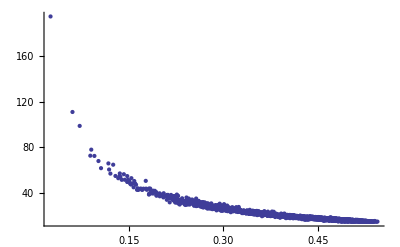

```mathematica
ListPlot[data]
```

```mathematica
FindFit[Select[data,#[[2]]≠-Infinity&], a x ^b,{a,b},x]
```

{a→9.06089,b→-0.86415}

```mathematica
FindFit[Select[data,#[[2]]≠-Infinity&], a x ^b,{a,b},x]
```

{a→9.15873,b→-0.869131}